```mathematica
xx = {x,y};
yy = {3,3};
q = 1;
Subscript[ϵ, 0] = 1;
a = 2;
l=0.2;
point = 80;
v1 = Sqrt[(xx-yy).(xx-yy)];
v2 = Sqrt[(xx-a^2/(yy.yy)yy).(xx-a^2/(yy.yy)yy)];
ϕ = (q/(4π Subscript[ϵ, 0]))/v1-(a q/(4π Subscript[ϵ, 0]))/(Sqrt[yy.yy] v2);
e = -Grad[ϕ,{x,y}];
points =Table[{l Cos[x(2Pi)/point]+yy[[1]],l Sin[ x(2Pi)/point]+yy[[2]]},{x,0,point}];
```

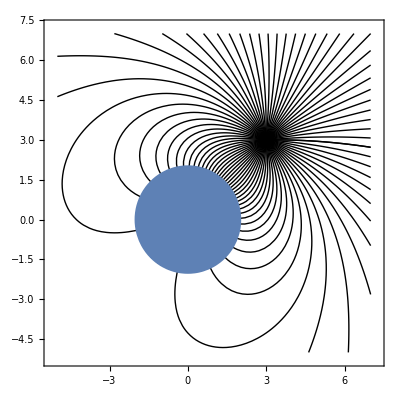

```mathematica
Show[{StreamPlot[e,{x,-5,7},{y,-5,7},StreamScale->None,RegionFunction->Function[{x,y},x^2+y^2>a^2],StreamPoints->{points,Automatic,Scaled[100]},
StreamStyle -> Black]},RegionPlot[x^2+y^2<a^2,{x,-5,5},{y,-5,5}, PlotStyle->Thick]]
```